## Boson Quadratic Hamiltonian

Calculating the Matrix Elements of H

## Subscript[H, b]=ϵb^+ b-v(b^+ b^++bb)

### Case |0>,|2>,|4>,...

```mathematica
dif[n_, m_] := n - m;
matEl02[n_, m_, e_, v_] := Piecewise[{{0, n==0&&m==0}, {e*m, dif[n,m]==0}, {√(m+1)√(m+2)*(-v), dif[n,m]==2}, {√m √(m-1)*(-v), dif[n,m]==-2}}];
```

```mathematica
Hmat02[n_, e_, v_] := 
  Table[Table[matEl02[2 (j - 1), 2 (i - 1), e, v], {i, 1, n}], {j, 1, n}];
```

```mathematica
Hmat02[6, e, v] // MatrixForm
```

(0 | -√2 v | 0 | 0 | 0 | 0
-√2 v | 2 e | -2 √3 v | 0 | 0 | 0
0 | -2 √3 v | 4 e | -√30 v | 0 | 0
0 | 0 | -√30 v | 6 e | -2 √14 v | 0
0 | 0 | 0 | -2 √14 v | 8 e | -3 √10 v
0 | 0 | 0 | 0 | -3 √10 v | 10 e)

```mathematica
Hmat02[6, e, v]/e // MatrixForm
```

(0 | -(√2 v)/e | 0 | 0 | 0 | 0
-(√2 v)/e | 2 | -(2 √3 v)/e | 0 | 0 | 0
0 | -(2 √3 v)/e | 4 | -(√30 v)/e | 0 | 0
0 | 0 | -(√30 v)/e | 6 | -(2 √14 v)/e | 0
0 | 0 | 0 | -(2 √14 v)/e | 8 | -(3 √10 v)/e
0 | 0 | 0 | 0 | -(3 √10 v)/e | 10)

```mathematica
redM02[n_, q_] := Hmat02[n, 1, q];
```

### Case |1>,|3>,|5>,...

```mathematica
matEl13[n_, m_, e_, v_] := Piecewise[{{0, n==0&&m==0}, {e*m, dif[n,m]==0}, {√(m+1)√(m+2)*(-v), dif[n,m]==2}, {√m √(m-1)*(-v), dif[n,m]==-2}}];
```

```mathematica
Hmat13[n_, e_, v_] := 
  Table[Table[matEl13[2 j + 1, 2 i + 1, e, v], {i, 0, n - 1}], {j, 0, n - 1}];
```

```mathematica
Hmat13[6, e, v] // MatrixForm
```

(e | -√6 v | 0 | 0 | 0 | 0
-√6 v | 3 e | -2 √5 v | 0 | 0 | 0
0 | -2 √5 v | 5 e | -√42 v | 0 | 0
0 | 0 | -√42 v | 7 e | -6 √2 v | 0
0 | 0 | 0 | -6 √2 v | 9 e | -√110 v
0 | 0 | 0 | 0 | -√110 v | 11 e)

```mathematica
Hmat13[6, e, v]/e // MatrixForm
```

(1 | -(√6 v)/e | 0 | 0 | 0 | 0
-(√6 v)/e | 3 | -(2 √5 v)/e | 0 | 0 | 0
0 | -(2 √5 v)/e | 5 | -(√42 v)/e | 0 | 0
0 | 0 | -(√42 v)/e | 7 | -(6 √2 v)/e | 0
0 | 0 | 0 | -(6 √2 v)/e | 9 | -(√110 v)/e
0 | 0 | 0 | 0 | -(√110 v)/e | 11)

```mathematica
redM13[n_, q_] := Hmat13[n, 1, q];
```

Solving the eigenvalue and eigenvector equation

## Case 1

```mathematica
redM02[4, q] // MatrixForm
```

(0 | -√2 q | 0 | 0
-√2 q | 2 | -2 √3 q | 0
0 | -2 √3 q | 4 | -√30 q
0 | 0 | -√30 q | 6)

### Calculating the eigenvalues

```mathematica
sols02[n_, q_] := N[Eigenvalues[redM02[n, q]]];
p02[n_, q_] := 
  ListPlot[sols02[n, q], Axes -> False, Frame -> True, Joined -> True, 
   PlotStyle -> {Red, Thick}, PlotMarkers -> Automatic, 
   PlotRange -> Automatic, FrameLabel -> {"i", "λi"}, 
   LabelStyle -> {18, Bold, Black, FontFamily -> "Times New Roman"}, Epilog -> 
      Inset[
     Framed[Style[StringTemplate["ϵ/v=``"][q], 20], 
      Background -> None, FrameStyle -> White], Scaled[{0.2, 0.3}]]];
Show[p02[4, 0.5]]
```

-Graphics-

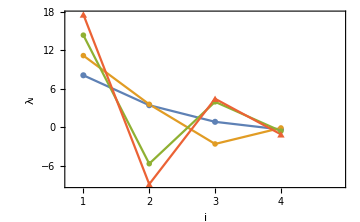

```mathematica
ListPlot[{sols02[4, 0.5], sols02[4, 1], sols02[4, 1.5], sols02[4, 2]}, 
 Joined -> True, Axes -> False, Frame -> True, PlotMarkers -> Automatic, 
 PlotRange -> {{0.8, 4.9}, Automatic}, 
 FrameLabel -> {"i", "\!\(\*SubscriptBox[\(λ\), \(i\)]\)"}, 
 LabelStyle -> {20, Bold, Black, FontFamily -> "Times New Roman"}, 
 ImageSize -> Medium]
```

## Case 2

```mathematica
redM13[4, q] // MatrixForm
```

(1 | -√6 q | 0 | 0
-√6 q | 3 | -2 √5 q | 0
0 | -2 √5 q | 5 | -√42 q
0 | 0 | -√42 q | 7)

### Calculating the eigenvalues

```mathematica
sols13[n_, q_] := N[Eigenvalues[redM13[n, q]]];
p13[n_, q_] := 
  ListPlot[sols13[n, q], Axes -> False, Frame -> True, Joined -> True, 
   PlotStyle -> {Red, Thick}, PlotMarkers -> Automatic, 
   PlotRange -> Automatic, FrameLabel -> {"i", "λi"}, 
   LabelStyle -> {18, Bold, Black, FontFamily -> "Times New Roman"}, Epilog -> 
      Inset[
     Framed[Style[StringTemplate["ϵ/v=``"][q], 20], 
      Background -> None, FrameStyle -> White], Scaled[{0.2, 0.3}]]];
Show[p13[4, 0.5]]
```

-Graphics-

```mathematica
ListPlot[{sols13[4, 0.5], sols13[4, 1], sols13[4, 1.5], sols13[4, 2]}, 
 Joined -> True, Axes -> False, Frame -> True, PlotMarkers -> Automatic, 
 PlotRange -> {{0.8, 4.9}, Automatic}, 
 FrameLabel -> {"i", "\!\(\*SubscriptBox[\(λ\), \(i\)]\)"}, 
 LabelStyle -> {20, Bold, Black, FontFamily -> "Times New Roman"}, 
 PlotLegends -> 
  Placed[{"\!\(\*FractionBox[\(ϵ\), \(v\)]\)=0.5", 
    "\!\(\*FractionBox[\(ϵ\), \(v\)]\)=1", 
    "\!\(\*FractionBox[\(ϵ\), \(v\)]\)=1.5", 
    "\!\(\*FractionBox[\(ϵ\), \(v\)]\)=2.5"}, {0.90, 0.5}], 
 ImageSize -> Large]
```

-Graphics-

## Lambdas - evolution with the ratio q

### Case 1: even k-bosonic states

```mathematica
lambdaId[n_,id_]:=Table[{q,sols02[n,q][[id]]},{q,0.05,3,0.1}];
```

```mathematica
myplot[n_,id_]:=ListPlot[lambdaId[n,id],Joined -> True, Axes -> False, Frame -> True, PlotMarkers -> Automatic, 
 PlotRange -> {Full, Full}, PlotStyle->{Red,Thick},
 FrameLabel -> {"q","λ[i](q)"}, 
 LabelStyle -> {20, Bold, Black, FontFamily -> "Times New Roman"},Epilog->{Inset[Framed[Style[StringTemplate["i=``"][id],20]],Scaled[{0.15,0.15}]],Inset[Framed[Style["0, 2, 4, ...",15]],Scaled[{0.85,0.15}]]},ImageSize->Medium];
```

```mathematica
Show[myplot[10,10]]
```

-Graphics-

```mathematica
Show[myplot[6,6]]
```

-Graphics-

```mathematica
Show[myplot[2,2]]
```

-Graphics-

```mathematica
Show[myplot[2,1]]
```

-Graphics-

```mathematica
Show[myplot[10,1]]
```

-Graphics-

```mathematica
Do[Print[sols02[5,q]],{q,0.01,1,0.1}]
```

{8.0028,5.9987,3.9991,1.9995,-0.00010001}

{8.30517,5.87793,3.8904,1.93875,-0.0122501}

{8.92951,5.73763,3.60988,1.76922,-0.0462374}

{9.69498,5.71129,3.22975,1.47164,-0.107654}

{10.527,5.78797,2.86035,1.03678,-0.212114}

{11.3952,5.93125,2.55904,0.523934,-0.409376}

{12.2851,6.11637,2.32297,-0.824494,0.100039}

{13.1893,6.32891,2.13371,-1.49306,-0.158863}

{14.1033,6.56033,-2.2896,1.97804,-0.35208}

{15.0244,6.8053,-3.14197,1.84846,-0.536164}

## Excited Spectrum of the Bosonic Hamiltonian

### Study of the eigenvalues of H (normalized to the first excited state)

## Normalize the eigenvalues to the first state

```mathematica
normal[data_]:=Table[data[[i]]/data[[1]],{i,1,Length[data]}];
```

## Case 1 - even bosonic states 0 2 4

```mathematica
proc02[n_,q_]:=Do[Print[StringTemplate["λ[``]=`` ; λ[``]=``"][id,sols02[n,q][[id]],id,normal[sols02[n,q]][[id]]]],{id,1, Length[sols02[n,q]]}];
```

```mathematica
proc02[10,0.5]
```

λ[1]=28.525 ; λ[1]=1.0

λ[2]=20.6939 ; λ[2]=0.725466

λ[3]=15.0612 ; λ[3]=0.528

λ[4]=10.7081 ; λ[4]=0.375395

λ[5]=7.27744 ; λ[5]=0.255125

λ[6]=4.58491 ; λ[6]=0.160733

λ[7]=2.52251 ; λ[7]=0.0884318

λ[8]=1.02294 ; λ[8]=0.0358614

λ[9]=-0.439808 ; λ[9]=-0.0154184

λ[10]=0.0438675 ; λ[10]=0.00153786

```mathematica
spectrum02[n_,id_]:=Table[{q,normal[sols02[n,q]][[id]]},{q,0.01,3,0.1}];
myplotnormal[n_,id_]:=ListPlot[spectrum02[n,id],Joined -> True, Axes -> False, Frame -> True, PlotMarkers -> Automatic, 
 PlotRange -> {Full, Full}, PlotStyle->{Red,Thick},
 FrameLabel -> {"q","λ[i](q)"}, 
 LabelStyle -> {20, Bold, Black, FontFamily -> "Times New Roman"},Epilog->{Inset[Framed[Style[StringTemplate["i=``"][id],20]],Scaled[{0.15,0.15}]],Inset[Framed[Style["0, 2, 4, ...",15]],Scaled[{0.85,0.15}]]},ImageSize->Medium];
```

```mathematica
Table[myplot[10,i],{i,2,10,2}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[myplotnormal[10,i],{i,2,10,2}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Hmat02[10,e,0]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 e | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4 e | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 6 e | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 8 e | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 10 e | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 12 e | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 14 e | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16 e | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 e)

```mathematica
Do[Print[Eigenvalues[Hmat02[10,e,0]][[id]]],{id,1,Length[Eigenvalues[Hmat02[10,e,0]]]}]
```

18 e

16 e

14 e

12 e

10 e

8 e

6 e

4 e

2 e

0

```mathematica
Table[myplotnormal[10,i],{i,1,6,1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Case 2 - odd bosonic states 1,3,5

```mathematica
proc13[n_,q_]:=Do[Print[StringTemplate["λ[``]=`` ; λ[``]=``"][id,sols13[n,q][[id]],id,normal[sols13[n,q]][[id]]]],{id,1, Length[sols13[n,q]]}];
```

```mathematica
proc13[10,0.5]
```

λ[1]=30.3064 ; λ[1]=1.0

λ[2]=22.291 ; λ[2]=0.735521

λ[3]=16.4908 ; λ[3]=0.544137

λ[4]=11.9748 ; λ[4]=0.395125

λ[5]=8.38035 ; λ[5]=0.276521

λ[6]=5.51992 ; λ[6]=0.182137

λ[7]=3.28288 ; λ[7]=0.108323

λ[8]=1.59941 ; λ[8]=0.0527747

λ[9]=0.424482 ; λ[9]=0.0140063

λ[10]=-0.270127 ; λ[10]=-0.0089132

```mathematica
spectrum13[n_,id_]:=Table[{q,normal[sols13[n,q]][[id]]},{q,0.01,3,0.1}];
myplotnormal13[n_,id_]:=ListPlot[spectrum13[n,id],Joined -> True, Axes -> False, Frame -> True, PlotMarkers -> Automatic, 
 PlotRange -> {Full, Full}, PlotStyle->{Red,Thick},
 FrameLabel -> {"q","λ[i](q)"}, 
 LabelStyle -> {20, Bold, Black, FontFamily -> "Times New Roman"},Epilog->{Inset[Framed[Style[StringTemplate["i=``"][id],20]],Scaled[{0.15,0.15}]],Inset[Framed[Style["1, 3, 5, ...",15]],Scaled[{0.85,0.15}]]},ImageSize->Medium];
```

```mathematica
Table[myplotnormal13[10,i],{i,1,6,1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}